```mathematica
Clear["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
recipesRaw=Import["recipe.json", "JSON"];
```

```mathematica
recipes=Association[#⟦1⟧->Association[#⟦2⟧]&/@recipesRaw];
(* remove some cycling recipes *)
recipes=Fold[Delete,recipes,ToUpperCase/@{
"basic-oil-processing",
"advanced-oil-processing",
"light-oil-cracking",
"heavy-oil-cracking",
"COAL-LIQUEFACTION",
"SOLID-FUEL-FROM-LIGHT-OIL",
"SOLID-FUEL-FROM-HEAVY-OIL",
"kovarex-enrichment-process"
}];
```

```mathematica
itemRecipeMapping=Association@Flatten@Map[
Function[recipe,
Map[
#->recipe⟦"name"⟧&,
recipe⟦"results",All,1⟧
]],
Values@recipes
];
hasItemRecipeQ[itemName_String]:=KeyExistsQ[itemRecipeMapping,itemName];
getItemRecipe[itemName_String?hasItemRecipeQ]:=recipes⟦itemRecipeMapping⟦itemName⟧⟧;
```

```mathematica
getRecipeInputEdges[recipe_]:=Map[{#⟦1⟧->recipe⟦"name"⟧,#⟦2⟧}&,recipe⟦"ingredients"⟧];
getRecipeOutputEdges[recipe_]:=Map[{recipe⟦"name"⟧->#⟦1⟧,#⟦2⟧}&,recipe⟦"results"⟧];
getRecipeEdges[recipe_]:=Join[getRecipeInputEdges[recipe],getRecipeOutputEdges[recipe]];
```

```mathematica
getItemIngredients[itemName_String]:=getRecipeInputEdges[getItemRecipe[itemName]]⟦All,1,1⟧;
```

```mathematica
getDependencyGraphHelper[itemName_String?hasItemRecipeQ]:=With[
{input=getItemIngredients[itemName]},
Join[
Map[#->itemName&,input],
Join@@Map[getDependencyGraphHelper,input]
]];
getDependencyGraphHelper[itemName_String]:={};

getDependencyGraph[itemName_String?hasItemRecipeQ]:=
getDependencyGraphHelper[itemName]//DeleteDuplicates;

getDependencyGraph[itemNames_List]:=
Join@@Map[getDependencyGraphHelper,itemNames]//DeleteDuplicates;
```

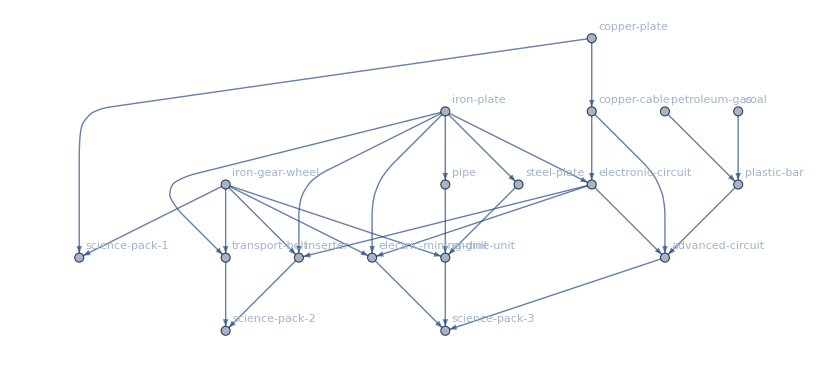

```mathematica
getDependencyGraph[{"science-pack-1","science-pack-2","science-pack-3"}];
With[{blacklist={
"iron-plate","copper-plate",
"iron-gear-wheel"
}},
Select[%,¬Or[
(*MemberQ[blacklist,#⟦1⟧],*)
MemberQ[blacklist,#⟦2⟧]
]&]];
Graph[%,VertexLabels->"Name",AspectRatio->Automatic]
```

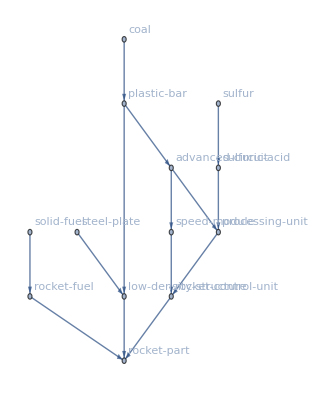

```mathematica
getDependencyGraph["rocket-part"];
With[{blacklist={
"iron-plate","copper-plate","water","electronic-circuit",
"petroleum-gas",
"iron-gear-wheel","copper-cable",
}},
Select[%,¬Or[
MemberQ[blacklist,#⟦1⟧],
MemberQ[blacklist,#⟦2⟧]
]&]];
Graph[%,VertexLabels->"Name",AspectRatio->Automatic]
```